## Load data

```mathematica
rand=Transpose[Flatten/@Import["00000_random_x000_y000.mat"]];
```

```mathematica
para=Transpose[Flatten/@Import["00001_parabolic_x000_y000.mat"]];
```

```mathematica
para0100=Transpose[Flatten/@Import["00001_parabolic_x010_y000.mat"]];
```

```mathematica
para0101=Transpose[Flatten/@Import["00001_parabolic_x010_y010.mat"]];
```

```mathematica
para0001=Transpose[Flatten/@Import["00001_parabolic_x000_y010.mat"]];
```

```mathematica
line=Transpose[Flatten/@Import["00161_lines1_x000_y000.mat"]];
```

```mathematica
line0001=Transpose[Flatten/@Import["00161_lines1_x000_y010.mat"]];
```

```mathematica
line0101=Transpose[Flatten/@Import["00161_lines1_x010_y010.mat"]];
```

```mathematica
line0100=Transpose[Flatten/@Import["00161_lines1_x010_y000.mat"]];
```

## Code

Gives the (numericized) maximum likelihood estimate of the cumulative probability of each unique member of the list l in sorted order. So, the list {3,2,3,3,3,3,2,1,3,3} would return {0.1,0.3,1.0} since the individiual entries (in order) have probabilities {0.1, 0.2,and 0.7}

```mathematica
cdf[l_List]:=N[Accumulate[Map[#[[2]]/Length[l]&,Sort[Tally[l],#1[[1]]<#2[[1]]&]]]]
```

```mathematica
cdf[{3,2,3,3,3,3,2,1,3,3}]
```

{0.1,0.3,1.}

```mathematica
pairWiseDistances[l_List]:=Map[l[[#+1]]-l[[#]]&,Range[Length[l]-1]]
```

```mathematica
nearestNeighborDistances[unsorted_List]:=With[{l=Sort[unsorted]},Which[
Length[l]==1,{0},
Length[l]==2,With[{d=l[[2]]-l[[1]]},{d,d}],
True,With[{pwd=pairWiseDistances[l]},
Flatten[{pwd[[1]],Map[Min[pwd[[#]],pwd[[#+1]]]&,Range[Length[pwd]-1]],pwd[[Length[pwd]]]}]
]
]]
```

```mathematica
nearestNeighborDistances[{1}]
```

{0}

```mathematica
nearestNeighborDistances[{1,2}]
```

{1,1}

```mathematica
nearestNeighborDistances[{1,2,8}]
```

{1,1,6}

```mathematica
nearestNeighborDistances[{1,2,2,8}]
```

{1,0,0,6}

Display the dependence measures with a specified number of bins (or dependence measure id) and sample size as a column containing: the sorted values and the number of occurrences for each, the cumulative probabilities of each value, and the same information displayed as a histogram.

```mathematica
analyzeSampleBinCombo[nSamples_,nBins_,xp_List]:=With[{deps=#[[1]]&/@Select[xp,#[[2]]==nBins && #[[4]]==nSamples&]},
Column[{Sort[Tally[deps],#1[[1]]<#2[[1]]&],
cdf[deps],nearestNeighborDistances[Union[deps]],Histogram[deps,100,"Probability",ImageSize->Large]},Frame->All]]
```

```mathematica
primesLessThanOrEqualTo[n_]:=Flatten[Which[
n<2,{},
PrimeQ[n],{n,primesLessThanOrEqualTo[NextPrime[n,-1]]},
True,primesLessThanOrEqualTo[NextPrime[n,-1]]
]]
```

```mathematica
primesLessThanOrEqualTo[10]
```

{7,5,3,2}

```mathematica
primesLessThanOrEqualTo[11]
```

{11,7,5,3,2}

```mathematica
allHistograms[nSamples_,xp_List,histFactor_]:=
With[{correctSampXP=Select[xp,#[[4]]==nSamples&]},
Column[
Map[Function[nBins,
Histogram[#[[1]]&/@Select[correctSampXP,#[[2]]==nBins&],histFactor,"Probability",PlotLabel->ToString[nSamples]~~" samples & "~~ToString[nBins]~~" bins",ImageSize->Medium,PlotRange->{0,1}]],
With[{primes=primesLessThanOrEqualTo[nSamples]},Complement[Range[4,nSamples],primes]]],Frame->All]]
```

```mathematica
allNonMICHistograms[nSamples_,xp_List]:=
With[{correctSampXP=Select[xp,#[[4]]==nSamples&]},
Column[
Map[Function[nBins,
Histogram[#[[1]]&/@Select[correctSampXP,#[[2]]==nBins&],Automatic,"Probability",PlotLabel->ToString[nSamples]~~" samples & method id="~~ToString[nBins],ImageSize->Medium]],
{1.,2.,3.}],Frame->All]]
```

## Noiseless Distributions

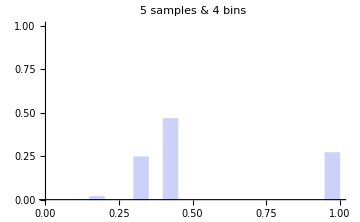
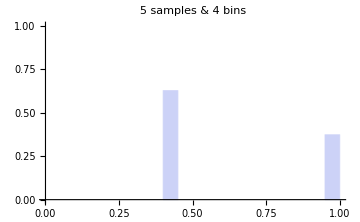
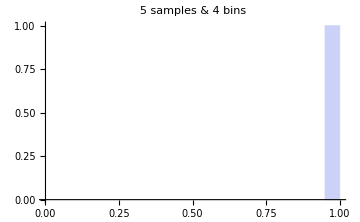

```mathematica
Row[{allHistograms[5,rand,20],allHistograms[5,para,20],allHistograms[5,line,20]}]
```

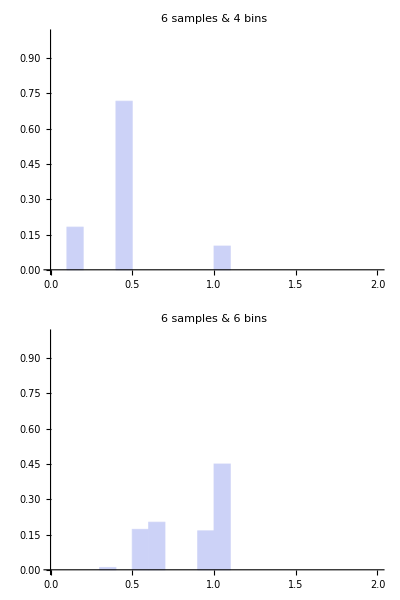
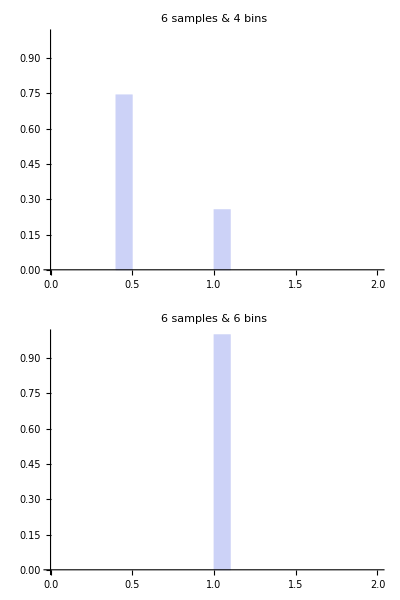
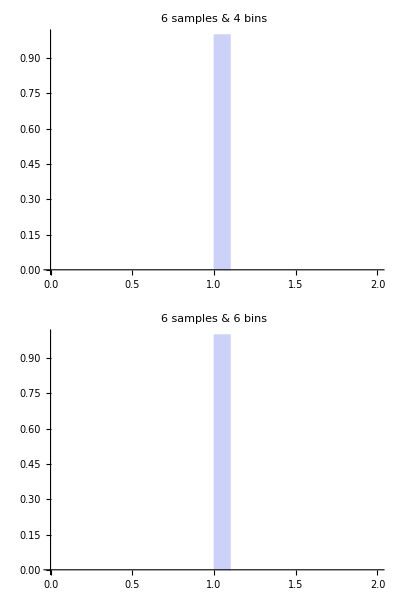

```mathematica
Row[{allHistograms[6,rand,20],allHistograms[6,para,20],allHistograms[6,line,20]}]
```

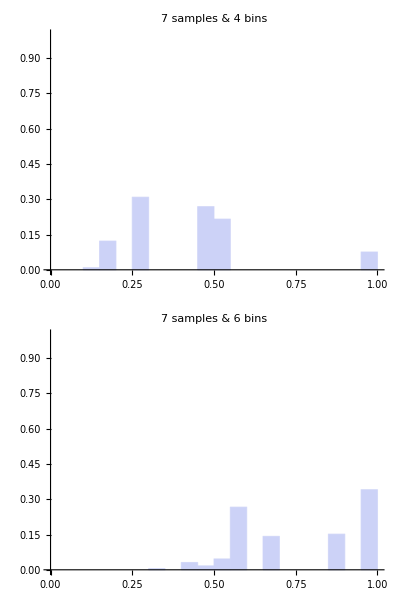
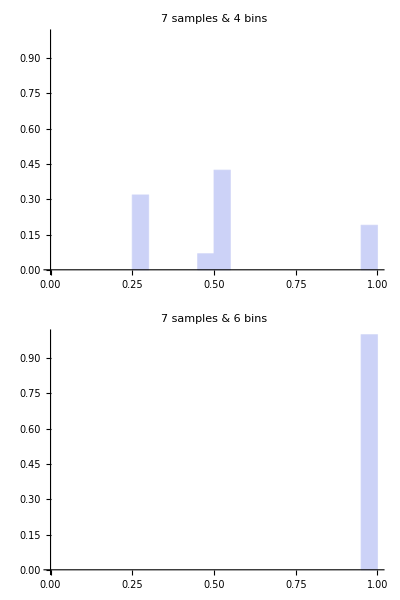
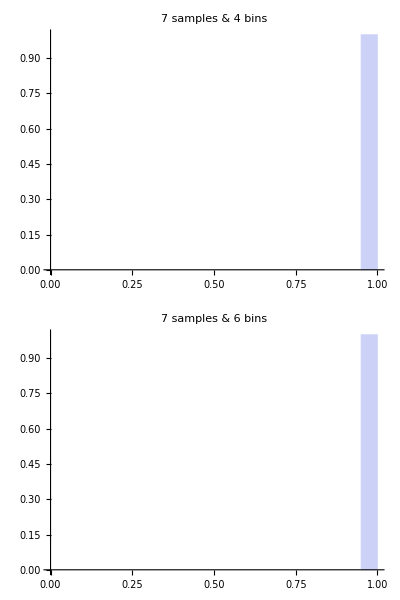

```mathematica
Row[{allHistograms[7,rand,20],allHistograms[7,para,20],allHistograms[7,line,20]}]
```

## Noisy line

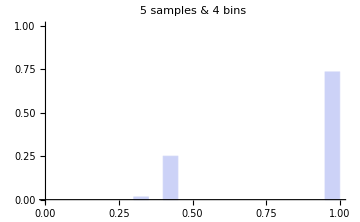
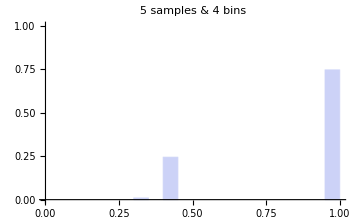
-Graphics--Graphics--Graphics-

```mathematica
Row[{allHistograms[5,rand,20],allHistograms[5,line0001,20],allHistograms[5,line0100,20]}]
```

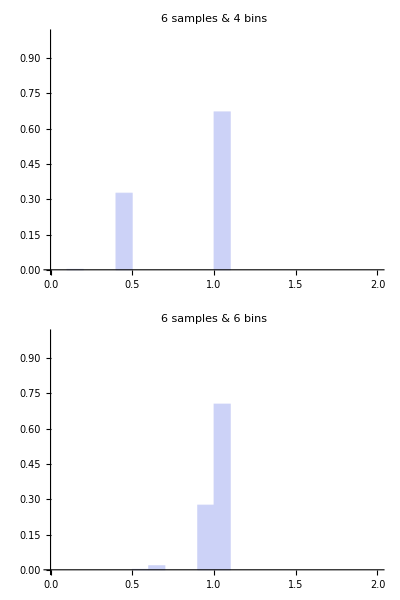
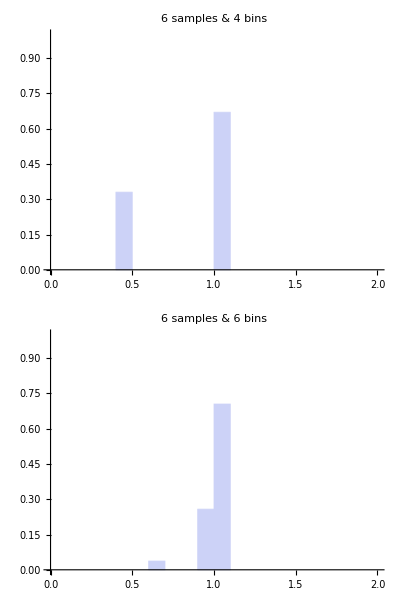
-Graphics--Graphics--Graphics-

```mathematica
Row[{allHistograms[6,rand,20],allHistograms[6,line0001,20],allHistograms[6,line0100,20]}]
```

## Noisy parabola

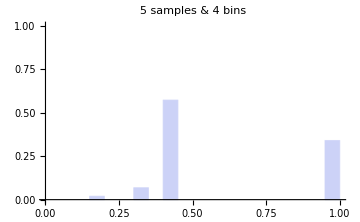
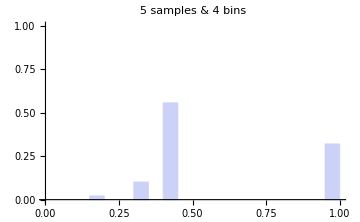
-Graphics--Graphics--Graphics-

```mathematica
Row[{allHistograms[5,rand,20],allHistograms[5,para0001,20],allHistograms[5,para0100,20]}]
```

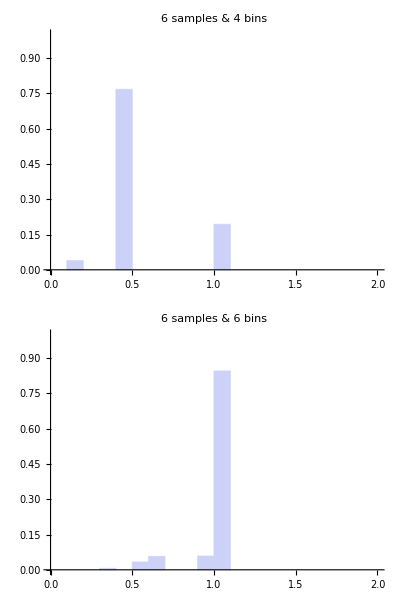
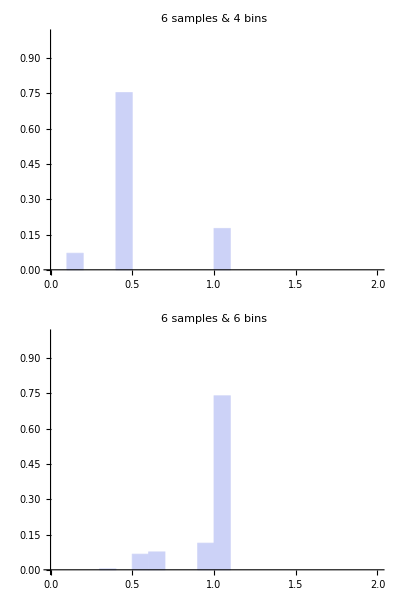
-Graphics--Graphics--Graphics-

```mathematica
Row[{allHistograms[6,rand,20],allHistograms[6,para0001,20],allHistograms[6,para0100,20]}]
```

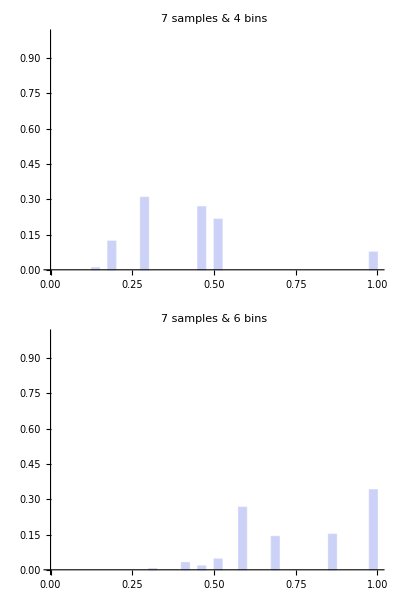
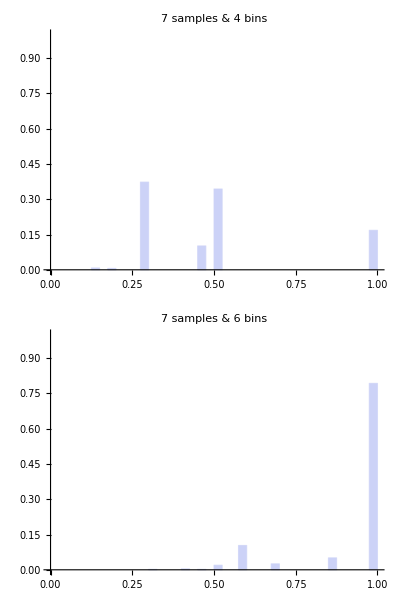
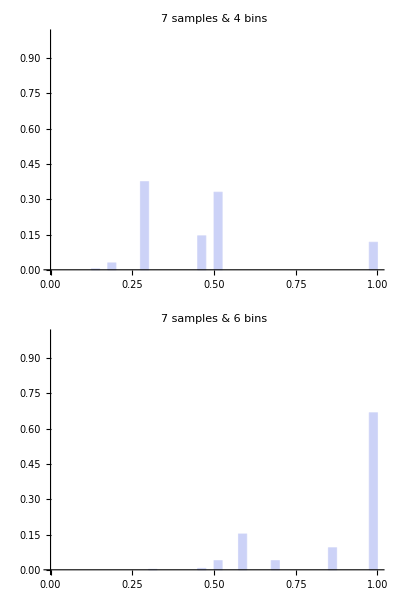

```mathematica
Row[{allHistograms[7,rand,40],allHistograms[7,para0001,40],allHistograms[7,para0100,40]}]
```

At 7 samples, 4 bins with the noisy parabola, we see an example where the mic scores that become more likely under a non-random input are not all in a row, so selecting mic values rather than a threshold can give an improvement. (The third highest score becomes less probable if non-random parabola, but the second and fourth become more probable)

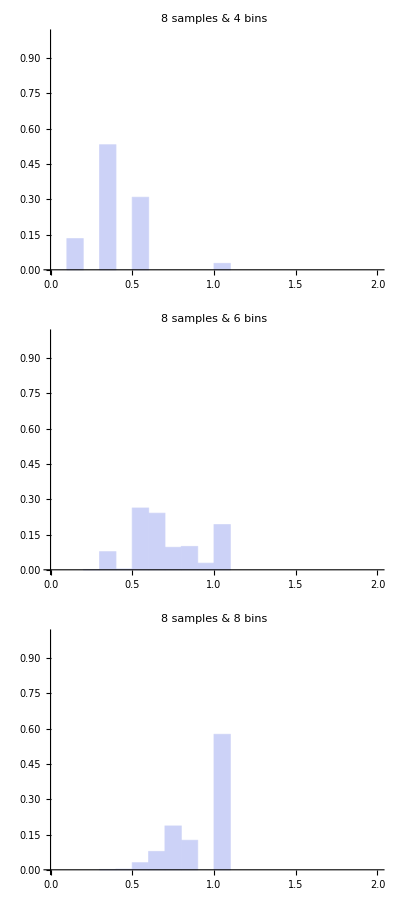
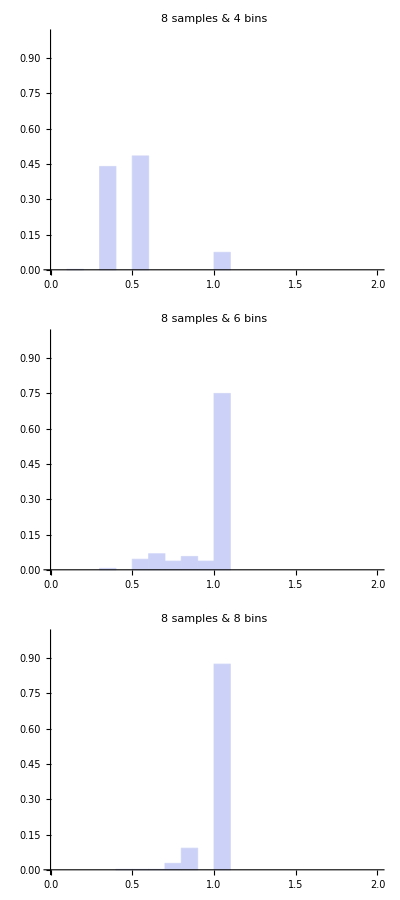
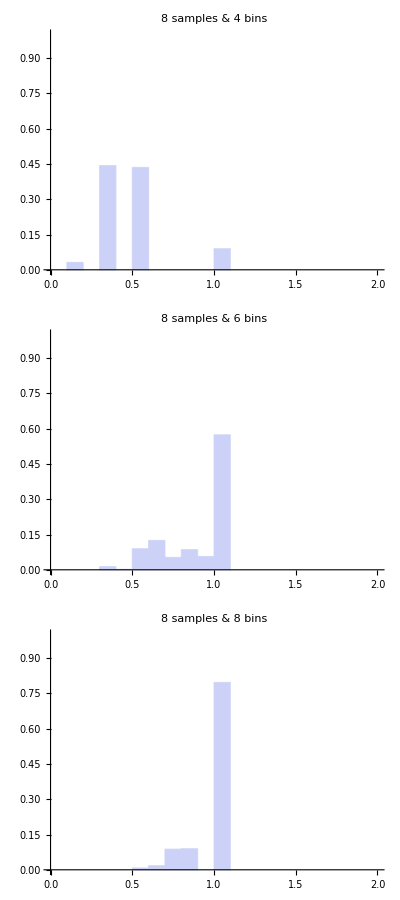

```mathematica
Row[{allHistograms[8,rand,20],allHistograms[8,para0001,20],allHistograms[8,para0100,20]}]
```

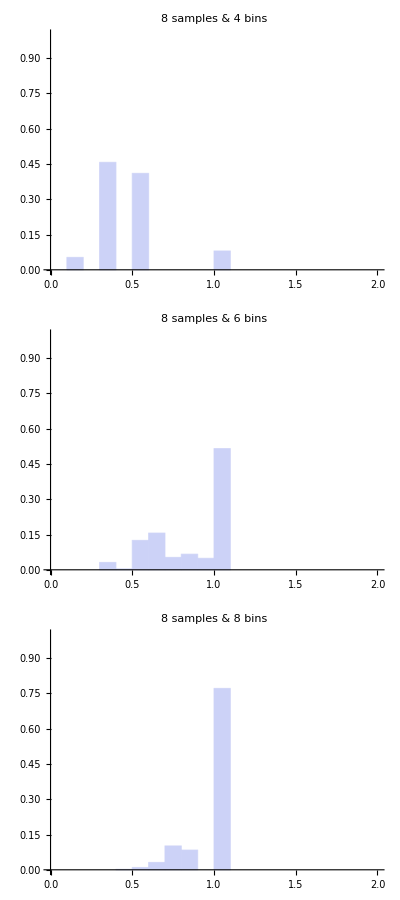
-Graphics--Graphics-

```mathematica
Row[{allHistograms[8,rand,20],allHistograms[8,para0101,20]}]
```